```mathematica
dn1:=r1*n1*(1-n1/k1+α*n2/k1-c2*n2*n2/k1);
dn2:=r2*n2*(1-n2/k2+β*n1/k2-c1*n1*n1/k2);
```

```mathematica
eq=Solve[{dn1==0,dn2==0},{n1,n2}];
eq
```

{{n1→0,n2→k2},«1»,{n1→β/(2 c1)-1/2 √(β^2/c1^2-(2 c1 c2 k2-c1 α-c2 β^2)/(3 c1^2 c2)-(«1»)/(«1»)-(2^(1/3) («1»-«1»+(«1»)^2))/(3 c1^2 c2 («1»)^(1/3))-(«7»+√(«1»))^(1/3)/(3 2^(1/3) c1^2 c2))+1/2 «1»,n2→«1»},{«1»},{«1»},{n1→0,n2→0},{n1→k1,n2→0}}

```mathematica
r1=r2=1;
k1=k2=1;
c1=.1;
c2=.1;
α:=β;
```

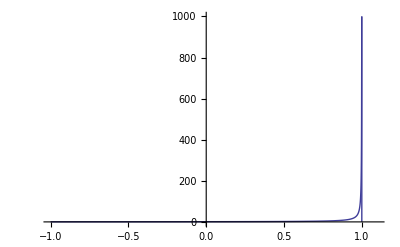

```mathematica
Plot[n1/.eq[[2]],{β,-1,1.1},PlotRange->{0,1000}]
```

```mathematica
Clear[α,β];
```

```mathematica
eq
```

{{n1→0,n2→1},{n1→2.,n2→2.},{n1→0,n2→0},{n1→1,n2→0}}

```mathematica
α=1.1;
β=1.1;
c1=0.1;
c2=0.1;
tmax=20;
r1 = 1.1;
r2 = 1.1;
k1 = 2;
k2 = 2;
sol=NDSolve[{
n1'[t]==r1*n1[t]*(1-n1[t]/k1+α*n2[t]/k1-c2*n2[t]*n2[t]/k1),
n2'[t]==r2*n2[t]*(1-n2[t]/k2+β*n1[t]/k2-c1*n1[t]*n1[t]/k2),
n1[0]==0.01,n2[0]==0.01},{n1,n2},{t,0,tmax}];
```

```mathematica
sol
```

{{n1→InterpolatingFunction[{{0.,20.}},<>],n2→InterpolatingFunction[{{0.,20.}},<>]}}

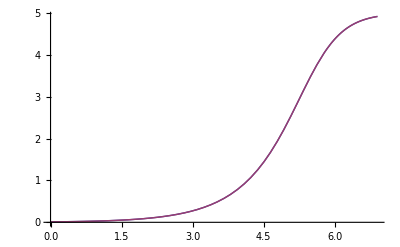

```mathematica
Plot[Evaluate[{n1[t],n2[t]}/.sol],{t,0,6.9},PlotRange->All]
```

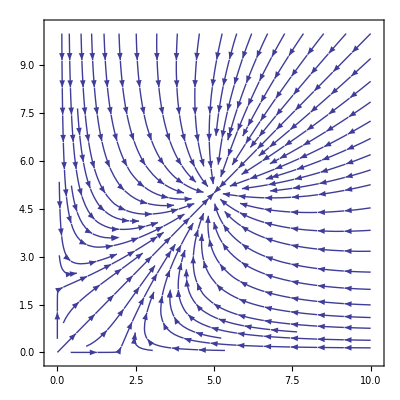

```mathematica
StreamPlot[{dn1,dn2},{n1,0,10},{n2,0,10}]
```

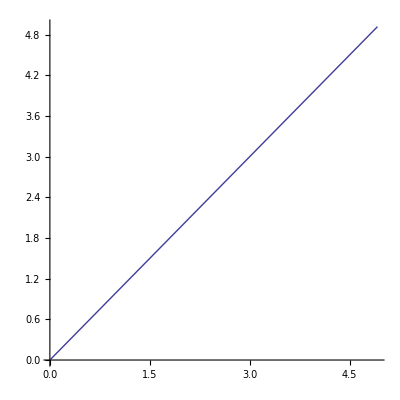

```mathematica
ParametricPlot[Evaluate[{n1[t],n2[t]}/.sol],{t,0,6.9},PlotRange->All]
```